```mathematica
<<"/Users/ethan/Desktop/WSS2017/saved_data/editInfo.mx"
<<"/Users/ethan/Desktop/WSS2017/saved_data/compData.mx"
```

```mathematica
template ={"https://tools.wmflabs.org/xtools-articleinfo/?article=","&project=en.wikipedia.org"};
urlForm = Flatten @ Table[StringReplace[i, " "-> "_"], {i, Keys[compData]}];
TitleToEdit[article_] :=Block[{}, 
	(*Print[template[[1]]<> article <> template[[2]]]; *)
	Import[template[[1]]<> article <> template[[2]], "Data"]
]
```

```mathematica
EditorStats[article_]:=
	If[
		Length@editInfo[article][[2]][[3]][[1]][[2;;]] ≤ 30,
		{Table[
			editInfo[article][[2]][[3]][[1]][[i]][[3]], {i, 2, Length@editInfo[article][[2]][[3]][[1]]}
		],
		Table[
			editInfo[article][[2]][[3]][[1]][[i]][[1]], {i, 2, Length@editInfo[article][[2]][[3]][[1]]}
		]},
		{Table[
			editInfo[article][[2]][[3]][[1]][[i]][[3]], {i, 2, 30}
		],
		Table[
			editInfo[article][[2]][[3]][[1]][[i]][[1]], {i, 2, 30}
		],
		editInfo[article][[2]][[3]][[1]][[32]]
		}
	]
editStats = AssociationMap[EditorStats,urlForm];
```

```mathematica
header = {"month","Number of edits","IPs","IPs %","Minor edits","Minor edits %"," All edits • IPs • Minor edits"};
EditDates[article_] :=
	Table[
		If[editInfo[article][[2]][[6]][[i]] ≠ header,
			Flatten@{
				DateObject[editInfo[article][[2]][[6]][[i]][[1]]],
				editInfo[article][[2]][[6]][[i]][[2;;]]
			},
			Nothing[]
		],
		{i, 1, Length@editInfo[article][[2]][[6]]}
	];
```

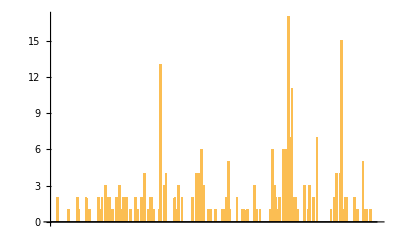

```mathematica
BarChart[EditDates["Computational_physics"][[All,2]]]
```